```mathematica
(* Kovaszny Flow - exact solution to NS equations *)
ClearAll[re,u,v,λ,p,pexact,x,y];
re=40;
xmin =-0.5;
xmax = 0.5;
ymin = -0.5;
ymax = 0.5;
pexact[x_]=(1-Exp[2 λ x])/2;
fx[x_]=D[pexact[x],x];
Print["d pexact / d x = ",fx[x]]
λ=re/2-Sqrt[re^2/4+4 π^2];
N[λ]


Print["pexact mean: ",Integrate[pexact[x],{x,-1/2,3/2}]/(1.5 + 0.5)]


u[x_,y_]=1-Exp[λ x] Cos[2 π y];
v[x_,y_]=(λ Exp[λ x] Sin[2 π y])/(2 π);
```

d pexact / d x = -ⅇ^(2 x λ) λ

-0.963741

pexact mean: 0.167185

```mathematica
umean[x_,y]=Sqrt[u[x,y]^2+v[x,y]^2];
```

```mathematica
Maximize[{umean[x,y],xmin<=x≤xmax,ymin≤y≤ymax},{x,y}]
```

{2.6191,{x→-0.5,y→0.5}}

```mathematica
Maximize[1-(x y-3)^2,{x,y}]
```

{1,{x→-1,y→-3}}

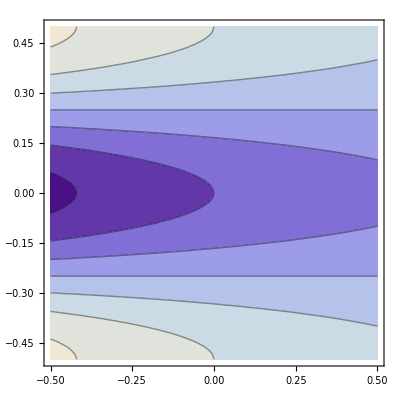

```mathematica
ContourPlot[u[x,y],{x,xmin,xmax},{y,ymin,ymax}]
```

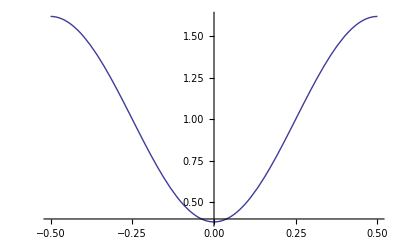

```mathematica
Plot[u[xmax,y],{y,ymin,ymax}]
```

```mathematica
(* Check for divergence free flow*)
Print["Divergence: ",Simplify[D[u[x,y],x]+ D[v[x,y],y]]]

(* integrated x-componentent of momentum equaiton *)
Print["X-momentum: ",FullSimplify[-u[x,y] D[u[x,y],x]-v[x,y] D[u[x,y],y]+1/re(D[u[x,y],{x,2}] + D[u[x,y],{y,2}])-D[pexact[x],x]]]

Print["Y-momentum: ",FullSimplify[-u[x,y] D[v[x,y],x]-v[x,y] D[v[x,y],y]+1/re(D[v[x,y],{x,2}] + D[v[x,y],{y,2}] - D[pexact[x],y])]]
```

Divergence: 0

X-momentum: 0

Y-momentum: 0

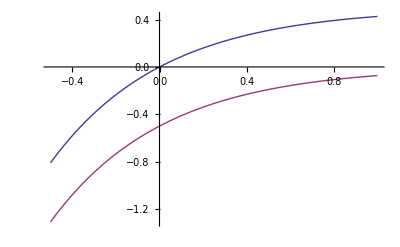

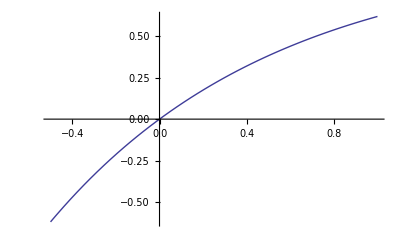

```mathematica
Plot[{pexact[x],-1/2 ⅇ^(-4 (-10+√(100+π^2)) x)},{x,-0.5,1}]
Plot[{u[x,0]},{x,-0.5,1}]
```

```mathematica
D[pexact[x],x]
```

-ⅇ^(2 (20-√(400+4 π^2)) x) (20-√(400+4 π^2))